```mathematica
SetDirectory[NotebookDirectory[]];
points = Import["project\\project\\in.txt", "Table"][[2;;]];
```

```mathematica
points;
```

```mathematica
points = Table[{RandomReal[{-20,20}],RandomReal[{-20,20}]},{i,200}];
```

```mathematica
MyLine[p1_, p2_, x_]:=(p2[[2]] - p1[[2]])/(p2[[1]] - p1[[1]])(x-p1[[1]]) + p1[[2]];
MyCheckPoint[p1_, p2_, p_]:=Module[{isUpperThanLine = True, x= p[[1]], ytrue, liney},
If[p1 == p || p2 == p,Return @Nothing];
If[p1[[1]] == p2[[1]] && x == p1[[1]], Return@Nothing];
If[p1[[1]]==p2[[1]],Return @(x > p1[[1]])];
ytrue = p[[2]];
liney = MyLine[p1,p2,x];
If[ytrue == liney, Return @Nothing];
 Return @(ytrue > liney);
]
MyCheckPoints[p1_, p2_,points_]:=Module[{positions},
positions = Table[MyCheckPoint[p1,p2,points[[k]]],{k,1,Length@points}];
positions[[0]] = Equal;
positions
]
MyEnumerate[pts_, allpts_]:=Module[{res,polygon,pairs},
pairs = Partition[Partition[Flatten[Table[{pts[[i]],pts[[j]]},{i,1,Length@pts},{j,i+1,Length@pts}]],2],2];
polygon = Cases[pairs, {p1_,p2_} /; MyCheckPoints[p1,p2,allpts]];
res = {polygon[[1]][[1]]};
res = res ~ Join ~ Table[polygon[[i]][[2]],{i,1,Length@polygon}];
res
]
Algo[pts_]:=Module[{points = pts, aboveline, underline, polygon1, polygon2, polygon},
points = Sort[points,#1[[1]]<#2[[1]]&];
aboveline = Cases[points, {x_, y_} /; y >= MyLine[points[[1]],points[[-1]],x]];
underline = Cases[points, {x_, y_} /; y < MyLine[points[[1]],points[[-1]],x]];
underline = Reverse@underline; 
AppendTo[underline,aboveline[[1]]];
polygon1 = MyEnumerate[aboveline, points];
polygon2 = MyEnumerate[underline, points];
polygon = polygon1 ~ Join ~ polygon2;
polygon
]
```

```mathematica
Timing[p = Algo[points];]
```

{49.5156,Null}

```mathematica
ClearSystemCache[];
Timing[p=Algo[points];]
```

{52.25,Null}

```mathematica
{{-1.8793754625930124,-0.10126241697157035},{-0.7836526852526244,0.9514304980836306},{1.0220494680093584,0.8693632531511741},{1.8306973684761827,0.2888380572214797},{1.918425267676298,0.1022527158522708},{1.918425267676298,0.1022527158522708},{1.6501204252210941,-0.9948838932996571},{-1.7266367519320331,-0.9257845176302815},{-1.8793754625930124,-0.10126241697157035}}
p = PrependTo[p, Length@p]
```

{{-1.87938,-0.101262},{-0.783653,0.95143},{1.02205,0.869363},{1.8307,0.288838},{1.91843,0.102253},{1.91843,0.102253},{1.65012,-0.994884},{-1.72664,-0.925785},{-1.87938,-0.101262}}

{16,{-19.8911,3.99955},{-19.4186,14.9696},{-15.6044,17.8553},{-5.18095,19.5628},{10.3734,19.7353},{16.5698,18.4382},{18.9233,15.5825},{19.9302,0.576933},{19.9953,-16.8245},{19.6963,-18.2135},{12.9073,-18.9515},{-5.15669,-19.8503},{-18.271,-19.911},{-19.2314,-19.6976},{-19.7961,-16.5986},{-19.8911,3.99955}}

```mathematica
Export["out_wm.txt",p[[]], "Table"]
```

out_wm.txt

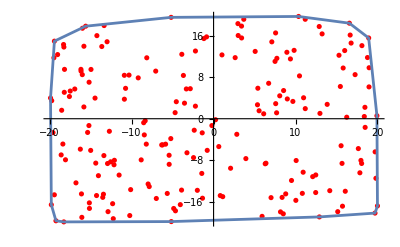

```mathematica
Show[ListPlot[points,PlotStyle->Red], ListLinePlot[p], PlotRange->All]
```